```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
massTestData=Import["first-Mass-vs-frequency-test.tsv"];
```

```mathematica
dipoleTestData=Import["/home/hyperion/Dropbox/Group Members/Taylor/Mass Scan/data/moment and mass.tsv"];
```

newCount[data_, initSampleSize_] --> counts how many particles were trapped per frequency. Divides by initial sample size if provided to give success rate

getMassVsFrequency --> grabs mass and frequency data from each trapped particle and stores as {frequency, mass} pairs.

getMassVsDipoleMoment --> grabs mass and dipole moment data, stores as {dipole moment, mass}.

sortByMass[data_,maxMass_,minMass_] and getCountVsMassVsFreq[data_,maxMass_,minMass_] --> sorts data into lists based on mass. The “bin size” is determined by the Δm factor in the sortByMass function. The getcount... function then combines these into a list of {frequency, mass, count} triplets to plot in 3D to visualize how success rate depends on both mass and frequency.

getVelocities[data_] -->Pretty straightforward. getVelocities and getPositions just grab the velocity or position data from a list.
getPositions[data_]

WILL HAVE TO CHANGE ALL OTHER FUNCTIONS BECAUSE THE OUTPUT DATA FORMAT IS NOW MUCH DIFFERENT

```mathematica
newCount[data_,initSampleSize_:1]:=Module[{countList={},count=0,i=1,freq},
freq=data⟦1,1⟧;
While[i≤Length[data],
If[data⟦i,1⟧==freq,count++];
If[data⟦i,1⟧≠freq,
AppendTo[countList,{freq,count/initSampleSize}];
freq=data⟦i,1⟧;
count=0];
i++;
];
AppendTo[countList,{freq,count/initSampleSize}];(*appends one last time to get final frequency's data*)
Return[countList]
]
```

```mathematica
getMassVsFrequency[data_]:=Module[{finalList=ConstantArray[0,Length[data]],i=1},
While[i≤Length[data],
finalList⟦i⟧={data⟦i,1⟧,data⟦i,2⟧};
i++;
];
Return[finalList]
]
```

```mathematica
getVelocities[data_]:=Module[{finalList},
finalList=data⟦All,{4,6}⟧*1000;
Return[finalList]
]
```

```mathematica
getPositions[data_]:=Module[{finalList},
finalList=data⟦All,{3,5}⟧;
Return[finalList]
]
```

```mathematica
getMassVsDipoleMoment[data_]:=Module[{finalList=ConstantArray[0,Length[data]],i=1},
While[i≤Length[data],
finalList⟦i⟧={data⟦i,3⟧,data⟦i,2⟧};
i++;
];
Return[finalList]
]
```

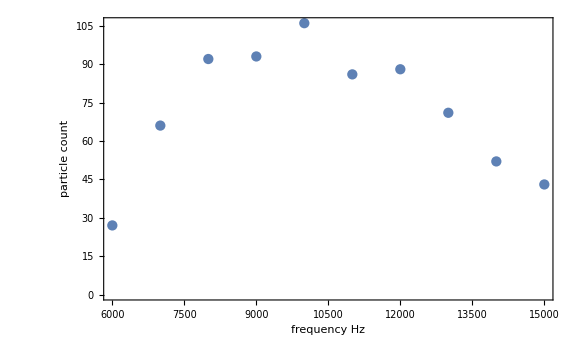

```mathematica
ListPlot[newCount[massTestData],ImageSize->Large,PlotRange->All,Joined->False,Frame->True,FrameLabel->{"frequency Hz","particle count"}]
```

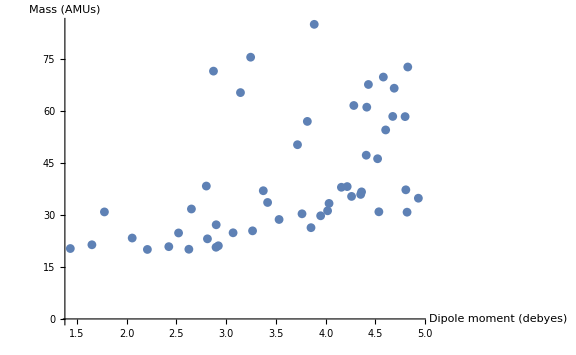

```mathematica
ListPlot[getMassVsDipoleMoment[dipoleTestData],ImageSize->Large,AxesLabel->{"Dipole moment (debyes)","Mass (AMUs)"}]
```

```mathematica
Clear[sortByMass];
sortByMass[data_,maxMass_,minMass_]:=Module[{Δm=10,finalList,massDiff,massQ,i=1,numOfGroups},
numOfGroups=Floor[(maxMass-minMass)/Δm];
finalList=ConstantArray[{},numOfGroups];
While[i≤Length[data],
massDiff=data⟦i,2⟧-minMass;
massQ=Quotient[massDiff,Δm]+1;(*plus one because need first index to be one*)
AppendTo[finalList⟦massQ⟧,data⟦i⟧];(*could change this to keep all original data*)
i++;
];
Return[finalList]
];
Clear[getCountVsMassVsFreq];
getCountVsMassVsFreq[data_,maxMass_,minMass_]:=Module[{finalList={},i=1,sortedData,mass,count},
sortedData=sortByMass[data,maxMass,minMass];
While[i≤Length[sortedData],
mass=Mean[sortedData⟦i,All,2⟧](*mass data point is average of list*);
count=newCount[sortedData⟦i⟧];
AppendTo[finalList,{count⟦#,1⟧,mass,count⟦#,2⟧}]&/@Range[1,Length[count]];
i++;
];
Return[finalList]
];
```

```mathematica
cmfData=Quiet[getCountVsMassVsFreq[massTestData,100,20]];
Quiet[ListPlot3D[cmfData,ImageSize->Large,Mesh->Automatic,PlotRange->All,AxesLabel->{"frequency","mass","count"}]]
```

-Graphics3D-

```mathematica
massSorted=sortByMass[massTestData,100,20];
```

```mathematica
vData=getVelocities/@massSorted;
```

```mathematica
posData=getPositions/@massSorted;
```

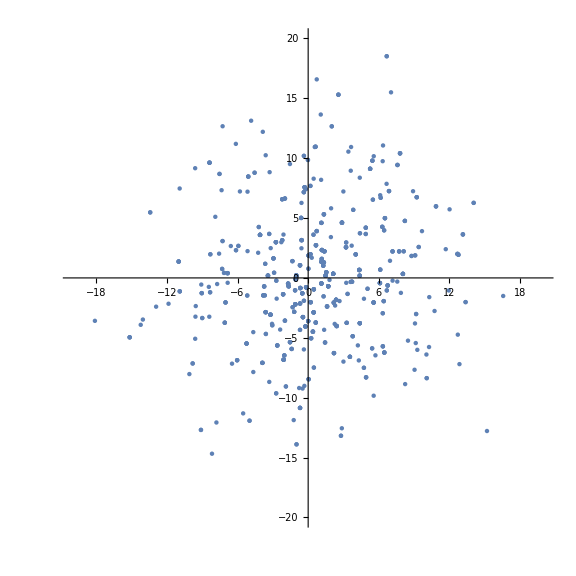

```mathematica
(*Plot of all velocities*)
ListPlot[getVelocities[massTestData],ImageSize->Large,PlotRange->{{-20,20},{-20,20}},AspectRatio->1]
```